```mathematica
rmax=3;r0=1;nindex=4/3;
Clear[b];
GetPoints[bval_]:=Module[{b=bval},
xystart={-rmax,b};
θ0=ArcSin[b/r0];
xy0={-r0*Cos[θ0],r0*Sin[θ0]};
(* Refraction *)
ϕ0=ArcSin[Sin[θ0]/nindex];
α0=θ0-ϕ0;
λ1=2*(Cos[α0]*Sqrt[1-b^2]+b*Sin[α0]);
x1=-Sqrt[1-b^2]+λ1*Cos[α0];
y1=b-λ1*Sin[α0];
xy1={x1,y1};
(* First reflection *)
β0=ArcTan[x1,y1];
γ1=π-α0-2*β0;
λ2=-2*(x1*Cos[γ1]-y1*Sin[γ1]);
x2=x1+λ2*Cos[γ1];
y2=y1-λ2*Sin[γ1];
xy2={x2,y2};
β1=ArcTan[x2,y2];
δ2=γ1+β1;
ϕ1=ArcSin[Sin[δ2]*nindex];
ϕ2=β1-ϕ1;
λ3=rmax-0.5;
x3=x2+λ3*Cos[ϕ2];
y3=y2+λ3*Sin[ϕ2];
xy3={x3,y3};
{{xystart,xy0,xy1,xy2,xy3},ϕ2}
]
```

{{-3,0.99},{-0.141067,0.99},{0.970299,0.241909},{0.340197,-0.940354},{-1.8672,-2.11397}}

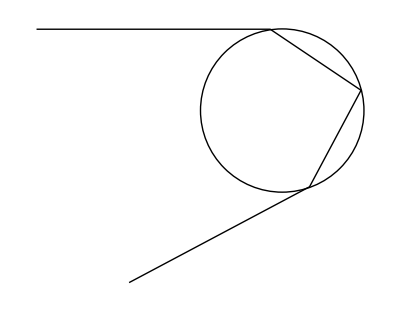

```mathematica
t0=Graphics[Circle[{0,0},r0]];
t1=GetPoints[0.99][[1]]
t2=Graphics[Line[t1]];
Show[t0,t2]
```

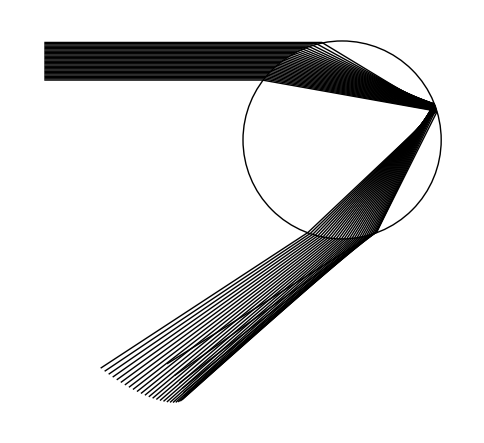

```mathematica
bpts=30;bmin=0.6;bmax=0.98;
bvals=Table[bmin+(bmax-bmin)*k/bpts,{k,0,bpts}];
lines=Table[Graphics[{Thin,Line[First@GetPoints@bvals[[k+1]]]}],{k,0,bpts}];
Show[lines,t0]
```

2.40804

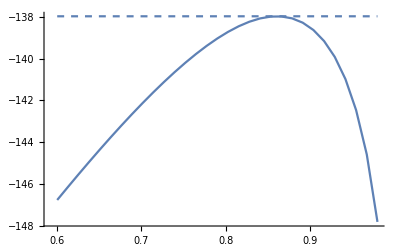

```mathematica
defl=Table[Last@GetPoints@bvals[[k+1]]*180/π,{k,0,bpts}];
plt1=ListPlot[Transpose@{bvals,defl},PlotRange->All,Joined->True];
huygens=N@2*ArcCos[1/nindex^2*((4-nindex^2)/3)^(3/2)]
huyg=-huygens*180/π;
plt2=Plot[huyg,{x,bmin,bmax},PlotStyle->Dashed];
Show[plt1,plt2]
```

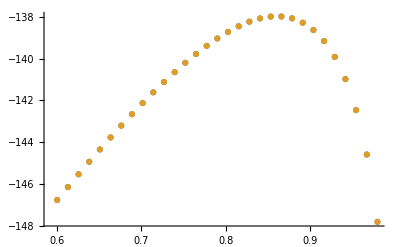

```mathematica
Clear[α];
Deflect[α_]:=π+2*α-4*ArcSin[Sin[α]/nindex];
defl2=N@Table[-Deflect[N@ArcSin[bvals[[k+1]] ]]*180/π,{k,0,bpts}];
ListPlot[{Transpose@{bvals,defl2},Transpose@{bvals,defl}}]
```

```mathematica
(* OK, so we can use the analytically-known formula *)
Deflector[α_]:=π+2*α-4*ArcSin[Sin[α]/n];
sol=Solve[D[Deflector[α],α]==0,α]
t0=N[α/.sol/.{n->nindex}]
bc=Sin[t0[[4]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-ArcCos[-(√(-1+n^2))/(√3)]},{α→ArcCos[-(√(-1+n^2))/(√3)]},{α→-ArcCos[(√(-1+n^2))/(√3)]},{α→ArcCos[(√(-1+n^2))/(√3)]}}

{-2.10502,2.10502,-1.03657,1.03657}

0.860663

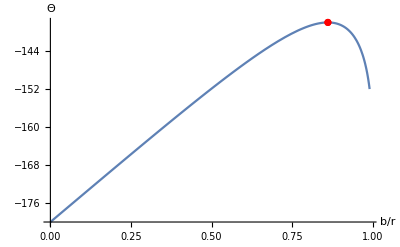

```mathematica
plt0=Plot[-Deflect[N@ArcSin[x]]*180/π,{x,0,0.99},AxesLabel->{b/r,Θ}];
plt1=ListPlot[{{bc,-Deflect[ArcSin[bc]]*180/π}},PlotStyle->Red];
Show[plt0,plt1]
```

```mathematica
nindex=4/3
Deflector[α_,k_]:=(k*π+2*α-2*(k+1)*ArcSin[Sin[α]/n]);
RadToDeg[val_]:=Mod[180.0*val/π/.{n->nindex},180];
(* From John A Adam *)
Clear[k,n];
ifn=ArcCos[Sqrt[(n^2-1)/(k*(k+2))]];
b1=N@Sin[ifn]/.{n->nindex,k->1};
b2=N@Sin[ifn]/.{n->nindex,k->2};
b3=N@Sin[ifn]/.{n->nindex,k->3};
D1=Deflector[ArcSin[b1],1]//RadToDeg;
D2=-Deflector[ArcSin[b2],2]//RadToDeg;
D3=Deflector[ArcSin[b3],3]//RadToDeg;
(*
D1=2*ArcCos[1/n^2*((4-n^2)/3)^(3/2)]/.{n->nindex}//N//RadToDeg
D2=2*ArcSin[Sqrt[n^2-1]*(Sqrt[9-n^2]/(2*n))^3]/.{n->nindex}//N//RadToDeg
D3=2*ArcCos[1/(5*(15)^(3/2))*(16-n^2)^(3/2)/n^4*(27*n^2-32)]/.{n->nindex}//N//RadToDeg
*)
plt1=Plot[{RadToDeg@Deflector[ArcSin[x],1],RadToDeg@(-Deflector[ArcSin[x],2]),RadToDeg@Deflector[ArcSin[x],3]},{x,0,0.999},AxesLabel->{b/r,Θ},PlotStyle->{Solid,Dashed,Dotted},PlotLabels->{"1 reflection",2,3}];
plt2=ListPlot[{{b1,D1},{b2,D2},{b3,D3}}];
Show[plt1,plt2]
```

4/3

-Graphics-